### Start choosing the example:

```mathematica
t=3;
beta=0;
A=0.2;
g[x]
```

Log[x]

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{}|>

```mathematica
Data["Switching Costs"] = {{1,2,3,S1},{3,2,1,S2}};
```

```mathematica
Data
```

<|Vertices List→{1,2},Adjacency Matrix→{{0,1},{0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{2,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->800,U1->15,S1->2,S2->3}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: {NonNegative[j6796]&&NonNegative[j6797]&&NonNegative[j6798]&&NonNegative[j6799]&&NonNegative[j6800]&&NonNegative[j6801]&&NonNegative[j6802]&&NonNegative[j6803]&&NonNegative[j6804]&&NonNegative[j6805]&&NonNegative[j6806]&&NonNegative[j6807]&&NonNegative[jt6808]&&NonNegative[jt6809]&&NonNegative[jt6810]&&NonNegative[jt6811]&&NonNegative[jt6812]&&NonNegative[jt6813]&&NonNegative[jt6814]&&NonNegative[jt6815]&&NonNegative[jt6816]&&NonNegative[jt6817]&&NonNegative[jt6818]&&NonNegative[jt6819]&&NonNegative[jt6820]&&NonNegative[jt6821]&&NonNegative[jt6822]&&NonNegative[jt6823]&&j6802==jt6808+jt6809&&j6803==jt6810+jt6811&&j6801==jt6812+jt6813&&j6796==jt6814&&j6804==jt6815&&j6797==jt6816&&j6805==jt6817&&j6798==jt6818+jt6819&&j6799==jt6820+jt6821&&j6806==jt6822+jt6823&&j6796==jt6810+jt6812&&j6797==jt6808+jt6813&&j6807==jt6809+jt6811&&j6802==jt6815&&j6798==jt6814&&j6803==jt6817&&j6799==jt6816&&j6804==jt6820+jt6822&&j6805==jt6818+jt6823&&j6800==jt6819+jt6821&&j6801==800&&u6834==15&&NonNegative[-u6824+u6825]&&NonNegative[u6824-u6825]&&NonNegative[u6824-u6835]&&NonNegative[u6825-u6835]&&NonNegative[2+u6826-u6830]&&NonNegative[-u6826+u6830]&&NonNegative[3+u6827-u6831]&&NonNegative[-u6827+u6831]&&NonNegative[-u6832+u6833]&&NonNegative[u6828-u6832]&&NonNegative[u6832-u6833]&&NonNegative[u6828-u6833]&&-u6829+u6835==0&&-u6828+u6834==0&&(j6802==0||j6796==0)&&(j6803==0||j6797==0)&&(j6804==0||j6798==0)&&(j6805==0||j6799==0)&&(j6806==0||j6800==0)&&(j6807==0||j6801==0)&&(jt6808==0||jt6810==0)&&(jt6809==0||jt6812==0)&&(jt6811==0||jt6813==0)&&(jt6814==0||jt6815==0)&&(jt6816==0||jt6817==0)&&(jt6818==0||jt6820==0)&&(jt6819==0||jt6822==0)&&(jt6821==0||jt6823==0)&&(jt6808==0||-u6824+u6825==0)&&jt6809==0&&(jt6810==0||u6824-u6825==0)&&jt6811==0&&(jt6812==0||u6824-u6835==0)&&(jt6813==0||u6825-u6835==0)&&(jt6814==0||2+u6826-u6830==0)&&(jt6815==0||-u6826+u6830==0)&&(jt6816==0||3+u6827-u6831==0)&&(jt6817==0||-u6827+u6831==0)&&(jt6818==0||-u6832+u6833==0)&&(jt6819==0||u6828-u6832==0)&&(jt6820==0||u6832-u6833==0)&&(jt6821==0||u6828-u6833==0)&&jt6822==0&&jt6823==0&&j6796-j6802-u6824+u6830==0&&j6797-j6803-u6825+u6831==0&&j6798-j6804-u6826+u6832==0&&j6799-j6805-u6827+u6833==0,{j6801→800,u6834→15}}

DataToEquations: The system is:
NonNegative[800-j6799+j6805+jt6820]&&NonNegative[j6799]&&NonNegative[800-j6799+j6805+jt6820]&&NonNegative[j6799]&&NonNegative[jt6820]&&NonNegative[j6805]&&NonNegative[jt6820]&&NonNegative[j6805]&&NonNegative[jt6820]&&NonNegative[j6805]&&NonNegative[800-j6799+jt6820]&&NonNegative[j6799-jt6820]&&NonNegative[800-j6799+j6805+jt6820]&&NonNegative[jt6820]&&NonNegative[j6799]&&NonNegative[j6805]&&NonNegative[j6805]&&NonNegative[800-j6799+jt6820]&&NonNegative[jt6820]&&NonNegative[j6799-jt6820]&&NonNegative[-u6824+u6825]&&NonNegative[u6824-u6825]&&NonNegative[u6824-u6829]&&NonNegative[u6825-u6829]&&NonNegative[802-j6799+j6805-u6824+u6826]&&NonNegative[-800+j6799-j6805+u6824-u6826]&&NonNegative[3+j6799-j6805-u6825+u6827]&&NonNegative[-j6799+j6805+u6825-u6827]&&NonNegative[800-2 j6799+2 j6805-u6826+u6827]&&NonNegative[815-j6799+j6805-u6826]&&NonNegative[-800+2 j6799-2 j6805+u6826-u6827]&&NonNegative[15+j6799-j6805-u6827]&&(jt6820==0||800-j6799+j6805+jt6820==0)&&(j6805==0||j6799==0)&&(jt6820==0||800-j6799+j6805+jt6820==0)&&(j6805==0||j6799==0)&&(jt6820==0||j6805==0)&&(800-j6799+j6805+jt6820==0||jt6820==0)&&(j6799==0||j6805==0)&&(j6805==0||jt6820==0)&&(jt6820==0||-u6824+u6825==0)&&(j6805==0||u6824-u6825==0)&&(800-j6799+jt6820==0||u6824-u6829==0)&&(j6799-jt6820==0||u6825-u6829==0)&&(800-j6799+j6805+jt6820==0||802-j6799+j6805-u6824+u6826==0)&&(jt6820==0||-800+j6799-j6805+u6824-u6826==0)&&(j6799==0||3+j6799-j6805-u6825+u6827==0)&&(j6805==0||-j6799+j6805+u6825-u6827==0)&&(j6805==0||800-2 j6799+2 j6805-u6826+u6827==0)&&(800-j6799+jt6820==0||815-j6799+j6805-u6826==0)&&(jt6820==0||-800+2 j6799-2 j6805+u6826-u6827==0)&&(j6799-jt6820==0||15+j6799-j6805-u6827==0)
and the rules are:
<|j6801→800,u6834→15,j6796→800-j6799+j6805+jt6820,j6797→j6799,j6798→800-j6799+j6805+jt6820,j6800→800,j6802→jt6820,j6803→j6805,j6804→jt6820,j6806→0,j6807→0,jt6808→jt6820,jt6809→0,jt6810→j6805,jt6811→0,jt6812→800-j6799+jt6820,jt6813→j6799-jt6820,jt6814→800-j6799+j6805+jt6820,jt6815→jt6820,jt6816→j6799,jt6817→j6805,jt6818→j6805,jt6819→800-j6799+jt6820,jt6821→j6799-jt6820,jt6822→0,jt6823→0,u6828→15,u6830→-800+j6799-j6805+u6824,u6831→-j6799+j6805+u6825,u6832→-800+j6799-j6805+u6826,u6833→-j6799+j6805+u6827,u6835→u6829|>

DataToEquations: It took 0.14031 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.177543,Null}

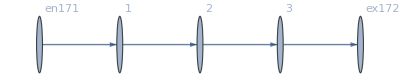

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j5761→800,j5762→800,j5763→800,j5764→0,j5765→0,j5766→0,jt5767→0,jt5768→800,jt5769→800,jt5770→0,u5771→815,u5772→15,u5773→815,u5774→15,u5775→15,u5776→815|>

#### Non-linear case

```mathematica
alpha=0;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→20.1639,u188→17.582,u189→15.,u190→20.1639,u191→17.582,u192→15.,u193→15.,u194→20.1639|>

```mathematica
alpha=0.1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→21.3227,u188→18.1613,u189→15.,u190→21.3227,u191→18.1613,u192→15.,u193→15.,u194→21.3227|>

```mathematica
alpha=0.3;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→25.0478,u188→20.0239,u189→15.,u190→25.0478,u191→20.0239,u192→15.,u193→15.,u194→25.0478|>

```mathematica
alpha=1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.20583×10^-13,ComplexInfinity]

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→175.,u188→95.,u189→15.,u190→175.,u191→95.,u192→15.,u193→15.,u194→175.|>

```mathematica
alpha=1.2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→742.811,u188→378.906,u189→15.,u190→742.811,u191→378.906,u192→15.,u193→15.,u194→742.811|>

```mathematica
alpha=1.6;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→580101.,u188→290058.,u189→15.,u190→580101.,u191→290058.,u192→15.,u193→15.,u194→580101.|>

```mathematica
alpha=1.7;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→3.119×10^7,u188→1.5595×10^7,u189→15.,u190→3.119×10^7,u191→1.5595×10^7,u192→15.,u193→15.,u194→3.119×10^7|>

```mathematica
alpha=1.8;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→4.81052×10^10,u188→2.40526×10^10,u189→15.,u190→4.81052×10^10,u191→2.40526×10^10,u192→15.,u193→15.,u194→4.81052×10^10|>

```mathematica
alpha=1.9;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→1.12074×10^19,u188→5.6037×10^18,u189→15.,u190→1.12074×10^19,u191→5.6037×10^18,u192→15.,u193→15.,u194→1.12074×10^19|>

```mathematica
alpha=2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j173→80,j174→80,j175→80,j176→80,j177→0.,j178→0.,j179→0.,j180→0.,jt181→0.,jt182→80,jt183→80,jt184→0.,jt185→80,jt186→0.,u187→4.4098×10^106,u188→2.2049×10^106,u189→15.,u190→4.4098×10^106,u191→2.2049×10^106,u192→15.,u193→15.,u194→4.4098×10^106|>